```mathematica
Clear[hv1,hv3,hv4,hv5,lwei,mwei,rwei];
Manipulate[Plot[Piecewise[{{hv1,-Infinity<x0<=-(lwei+mwei/2)},
{0,-(lwei+mwei/2)<x0≤-(mwei/2)},
{hv3,-(mwei/2)<x0<=(mwei/2)},
{hv4,-(mwei/2)<x0<=(rwei+mwei/2)},
{hv5,(rwei+mwei/2)<x0<Infinity}}],
{x0,-(lwei+mwei/2)*2,(rwei+mwei/2)*2},PlotRange->{-Max[hv1,hv3,hv5]*0.5,Max[hv1,hv3,hv5]*1.5},PlotStyle->Blue,Exclusions->None,PlotPoints->300],
{{hv1,10,"hv1_区域1阱高/meV"},0.1,100,1},
{{hv3,8,"hv3_中间区域3阱高/meV"},0,100,1},
{{hv4,5,"hv4_区域4阱高/meV"},0,100,1},
{{hv5,12,"hv5_区域5阱高/meV"},0,100,1},
{{lwei,4,"左阱宽/nm"},0.1,100,0.01},
{{mwei,2,"阱距/nm"},0,100,0.01},
{{rwei,3,"右阱宽/nm"},0,100,0.01},
LocalizeVariables->False]
```

势垒高度（meV）：
{9.1,0.,6.,4.5,12.}

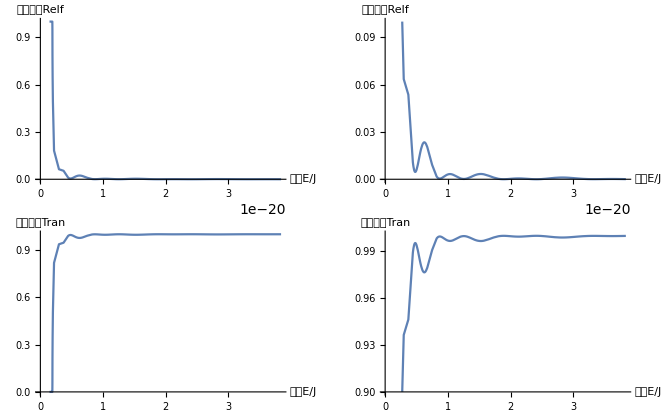

```mathematica
Clear[As,At,V,K];
Clear[hb,me,e,V01,V02,V03,V04,V05,Vso];
Clear[a1,b1,c1];
Clear[t,J,hb,me];

t=10^(-9);(*1纳米*)
J=1.6*10^(-22);(* 1毫电子伏特*)
me=9.1*10^(-31);(*单位：kg*)
hb=6.626*10^(-34)/(2*Pi)(*单位 J*s *);
a1=(mwei/2)*t;
b1=(lwei+mwei/2)*t;
c1=(rwei+mwei/2)*t;


V01=J*hv1;
V02=J*0;
V03=J*hv3;
V04=J*hv4;
V05=J*hv5;

Vso=Sort[{V01,V03,V04,V05}]/J;
Vmin=Vso[[3]]*J;
Vmax=Vso[[4]]*J;

(*Print["Vmin   ",Vmin*2]
e=Vmin*2*)

V={V01,0,V03,V04,V05};
X={-(a1+b1),-a1,a1,a1+c1};

(*五个区域的波矢*)
K=Table[ks,5];
For[i=1,i<6,i++,
K[[i]]=Sqrt[2*me(e-V[[i]])]/hb];

(*前n+1个界面的反射和透射振幅，共n+2个区域*)
At=Table[Ati,4];
As=Table[Asi,4];
(*最后一个界面的透射振幅和反射振幅*)
At[[4]]=E^(-I*K[[4]]*X[[4]])*(1+K[[5]]/K[[4]]);
As[[4]]=E^(I*K[[4]]*X[[4]])*(1-K[[5]]/K[[4]]);
(*递推透射振幅和反射振幅*)
For[i=3,i>=1,i--,
At[[i]]=E^(-I*K[[i]]*X[[i]])*(E^(I*K[[i+1]]*X[[i]])*(1+K[[i+1]]/K[[i]])*At[[i+1]]+E^(-I*K[[i+1]]*X[[i]])*(1-K[[i+1]]/K[[i]])*As[[i+1]]);

As[[i]]=E^(I*K[[i]]*X[[i]])*(E^(I*K[[i+1]]*X[[i]])*(1-K[[i+1]]/K[[i]])*At[[i+1]]+E^(-I*K[[i+1]]*X[[i]])*(1+K[[i+1]]/K[[i]])*As[[i+1]]);
];

Clear[Relf,Tran];
Relf=Chop[(As[[1]]*Conjugate[As[[1]]])/(At[[1]]*Conjugate[At[[1]]])];
Tran=1-Relf;

Print["势垒高度（meV）：","\n",V/J]
(*Print["能量","\n",e/J]*)

(*Print["波矢","\n",K];
Print["透射振幅","\n",At]
Print["反射振幅","\n",As]

Print["反射系数","\n",Relf]
Print["透射系数","\n",Tran]*)

pr1=Plot[Chop[(As[[1]]*Conjugate[As[[1]]])/(At[[1]]*Conjugate[At[[1]]])],{e,Vmin,20*Vmax},PlotRange->{0,1},AxesLabel->{Style["能量E/J",Bold,Black],Style["反射系数Relf",Bold,Black]}];
pt1=Plot[1-Chop[(As[[1]]*Conjugate[As[[1]]])/(At[[1]]*Conjugate[At[[1]]])],{e,Vmin,20*Vmax},PlotRange->{0,1},AxesLabel->{Style["能量E/J",Bold,Black],Style["透射系数Tran",Bold,Black]}];

pr2=Plot[Chop[(As[[1]]*Conjugate[As[[1]]])/(At[[1]]*Conjugate[At[[1]]])],{e,Vmin,20*Vmax},PlotRange->{0,0.1},AxesLabel->{Style["能量E/J",Bold,Black],Style["反射系数Relf",Bold,Black]}];
pt2=Plot[1-Chop[(As[[1]]*Conjugate[As[[1]]])/(At[[1]]*Conjugate[At[[1]]])],{e,Vmin,20*Vmax},PlotRange->{0.9,1.001},AxesLabel->{Style["能量E/J",Bold,Black],Style["透射系数Tran",Bold,Black]}];
GraphicsGrid[{{pr1,pr2},{pt1,pt2}},Frame->All]
```

```mathematica
3.5*10^-20/J
```

218.75

```mathematica
218.74999999999997/12
```

18.2292

```mathematica
10*J
```

1.6×10^-21